The following function generates the ‘empty’ grid with only the boundary cells filled in. Internal cells carry the value -1.

```mathematica
initialGridBorder[n_] := initialGridBorder[n] = Normal[SparseArray[{{i_, j_} /; i == 1 || j == 1 -> i + j - 2, {i_, j_} /; i == n || j == n -> 2n - i - j}, {n, n}, -1]]
```

The following shows an example of a 9 x 9 boundary grid:

Drag the slider to see larger grids.

```mathematica
colourRules={0->Red,1->Yellow,2->Blue};
Manipulate[ArrayPlot[initialGridBorder[3(2k - 1)]],{k,1,20,1}]
```

```mathematica
(* Helper function for generateMaxHeightGrid. Fills one concentric square of cells. *)
fillConcentricSquareMax[Hold[grid_], k_] := (
 grid[[k, k ;; -k]] = grid[[k - 1, k ;; -k]] + 1; 
 grid[[-k, k ;; -k]] = grid[[-(k - 1), k ;; -k]] + 1;
 grid[[k ;; -k, k]] = grid[[k ;; -k, k - 1]] + 1; 
 grid[[k ;; -k, -k]] = grid[[k ;; -k, -(k - 1)]] + 1; 
ReleaseHold[Hold[grid]])

(* Helper function for generateMinHeightGrid. Fills one concentric square of cells. *)
fillConcentricSquareMin[Hold[grid_], k_] := (
 grid[[k, k ;; -k]] = grid[[k - 1, k ;; -k]] - 1; 
 grid[[-k, k ;; -k]] = grid[[-(k - 1), k ;; -k]] - 1;
 grid[[k ;; -k, k]] = grid[[k ;; -k, k - 1]] - 1; 
 grid[[k ;; -k, -k]] = grid[[k ;; -k, -(k - 1)]] - 1; 
ReleaseHold[Hold[grid]])

(* Generates the grid with maximum height by starting from the boundary and moving inwards, filling in concentric squares. *)
generateMaxHeightGrid[dim_] := generateMaxHeightGrid[dim] = Module[{k = 1, depth = (dim + 1) / 2},
 Nest[( k++; currGrid = #; fillConcentricSquareMax[Hold[currGrid], k]; initialGrid = currGrid ) &, initialGrid = initialGridBorder[dim], depth - 1];
 Normal[initialGrid]
]

(* Generates the grid with minimum height by starting from the boundary and moving inwards, filling in concentric squares. *)
generateMinHeightGrid[dim_] := generateMinHeightGrid[dim] = Module[{k = 1, depth = (dim + 1) / 2},
 Nest[( k++; currGrid = #; fillConcentricSquareMin[Hold[currGrid], k]; initialGrid = currGrid ) &, initialGrid = initialGridBorder[dim], depth - 1];
 Normal[initialGrid]
]

(* Takes a grid with a filled in height function as input and converts it to its corresponding 3-colouring form. *)
to3Colouring[grid_] := Mod[grid, 3]

findListHeight[first_, list_, len_] := Module[{initialList = SparseArray[{}, {len}, -1], k = 0, prev = first}, (* remember that list is of length (len + 1) *)
 Nest[(k++; newList = #; prev = If[MemberQ[list[[{k, k + 1}]], 1], prev + list[[k + 1]] - list[[k]], If[list[[k]] == 2, prev + 1, prev - 1]]; newList[[k]] = prev; newList ) & , Normal[initialList], len]
]

(* Takes a 3-coloured grid as input and returns the corresponding grid labelled with its height values. *)
(* Note: this starts with the initial border grid *)
toHeightFunction[grid_, dim_] := Module[{heightGrid = initialGridBorder[dim], k = 1},
Nest[(k++; nextHeightGrid = #; nextHeightGrid[[k, 2 ;; -2]] = findListHeight[heightGrid[[k, 1]], Normal[grid[[k, 1 ;; -2]]], dim - 2]; nextHeightGrid) &, heightGrid, dim - 2] 
]
```

```mathematica
MatrixForm[toHeightFunction[to3Colouring[generateMaxHeightGrid[7]], 7]]
```

(0 | 1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 3 | 4 | 5 | 6 | 5
2 | 3 | 4 | 5 | 6 | 5 | 4
3 | 4 | 5 | 6 | 5 | 4 | 3
4 | 5 | 6 | 5 | 4 | 3 | 2
5 | 6 | 5 | 4 | 3 | 2 | 1
6 | 5 | 4 | 3 | 2 | 1 | 0)

See the max height grids and their corresponding 3-colourings for different side lengths. Dark cells are the highest, while white cells are at height 0:

```mathematica
Manipulate[ArrayPlot[generateMaxHeightGrid[3(2k - 1)]],{k,1,10,1}]
Manipulate[ArrayPlot[Mod[generateMaxHeightGrid[3(2k - 1)], 3],  ColorFunction->"CandyColors"], {k,1,10,1}]
```

See the min height grids and their corresponding 3 - colourings for different side lengths . Dark cells are the highest, while white cells are at height 0 :

```mathematica
Manipulate[ArrayPlot[generateMinHeightGrid[3(2k - 1)]],{k,1,10,1}]
Manipulate[ArrayPlot[Mod[generateMinHeightGrid[3(2k - 1)], 3],  ColorFunction->"CandyColors"], {k,1,10,1}]
```

```mathematica
selectRandomCell[dim_] := RandomChoice[Tuples[Range[2, dim - 1], 2]];
coinFlip[] := RandomChoice[{True, False}]
changeColour[grid_, pos_, newVal_] := ReplacePart[grid, pos -> newVal]

(* Check if you can pop up a cell at pos in grid. Works on both height values and 3-colourings *)
checkPopUp[grid_, pos_] := AllTrue[grid[[pos[[1]] + {-1, 1}, pos[[2]]]] ~ Join ~ grid[[pos[[1]], pos[[2]] + {-1, 1}]], Mod[grid[[Sequence @@ pos]] - #, 3] == 2 &]
(* Check if you can pop down a cell at pos in grid. Works on both height values and 3-colourings *)
checkPopDown[grid_, pos_] := AllTrue[grid[[pos[[1]] + {-1, 1}, pos[[2]]]] ~ Join ~ grid[[pos[[1]], pos[[2]] + {-1, 1}]], Mod[grid[[Sequence @@ pos]] - #, 3] == 1 &]

(* If heads, check if site can be popped up; otherwise, check if site can be popped down. *)
coinFunctionAssociation = Association[True -> checkPopUp, False -> checkPopDown];
coinSignAssociation = Association[True -> Plus, False -> Subtract];

(*  *)
 oneStep[dim_, maxGrid_, minGrid_] := Module[{site = selectRandomCell[dim], coin = coinFlip[], initialGrids = {maxGrid, minGrid}, outGrids = {maxGrid, minGrid}},
 Map[If[coinFunctionAssociation[coin][initialGrids[[#]], site], 
 (outGrids[[#]] = changeColour[initialGrids[[#]], site, Mod[coinSignAssociation[coin][initialGrids[[#]][[Sequence @@ site]], 2], 3]];)] &, {1, 2}];
 outGrids
 ]
```

```mathematica
viewChangeSteps[n_, maxGrid_, minGrid_, steps_] := (gridsList = NestList[oneStep[n, Sequence @@ #] &, {maxGrid, minGrid}, steps]; 
Manipulate[Grid[{{ArrayPlot[gridsList[[k]][[1]], ColorFunction->"CandyColors", Frame->True], ArrayPlot[gridsList[[k]][[2]], ColorFunction->"CandyColors", Frame->True]}}],{k,1,steps,1}])

checkHeightDifference[n_, maxGrid_, minGrid_] := Total[Table[Abs[maxGrid[[i, j]] - minGrid[[i, j]]], {i, 2, n - 1}, {j, 2, n - 1}], 2]

viewAfterSteps[n_, maxGrid_, minGrid_, steps_, logInterval_, prevStep_] := Module[{step = prevStep},
  PrintTemporary[ProgressIndicator[Dynamic[step/(steps + prevStep)]]]; {time, finalGrids} = AbsoluteTiming[Catch[Nest[(
  If[Mod[step, logInterval] == 0 || #[[1]] == #[[2]], (Export[StringJoin[ToString[NotebookDirectory[]], "output files/coupling_", ToString[n], "/log_", ToString[step], ".mx"], #]; 
    Print[checkHeightDifference[n, #[[1]], #[[2]]]])]; 
  If[#[[1]] == #[[2]], Throw[#]]; 
  step++; 
  oneStep[n, Sequence @@ #]) &, 
  {maxGrid, minGrid}, steps + 1]]];
  {time, step, finalGrids}
]

displayTime[time_] := DateString[time, {"Hour", ":", "Minute", ":", "Second"}]
```

```mathematica
ListPlot3D[generateMaxHeightGrid[81]]
ListPlot3D[generateMinHeightGrid[81]]
ListPlot3D[toHeightFunction[Import[NotebookDirectory[], "output files/coupling_81/log_85402849.mx"][[1]], 81]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
dim = 101;
maxGrid = to3Colouring[generateMaxHeightGrid[dim]];
minGrid = to3Colouring[generateMinHeightGrid[dim]];
checkHeightDifference[dim, maxGrid, minGrid]
```

8875

```mathematica
viewChangeSteps[dim, maxGrid, minGrid, 10000]
```

```mathematica
dim = 81;
(*grid1 = to3Colouring[generateMaxHeightGrid[dim]];
grid2 = to3Colouring[generateMinHeightGrid[dim]];*)
(* NOTE: change input and stagger! *)
{grid1, grid2} = Import[NotebookDirectory[], "output files/coupling_81/log_57000000.mx"];
{time, step, {final1, final2}} = viewAfterSteps[dim, grid1, grid2, 100000000, 1000000, 57000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final1, ColorRules -> colourRules, Frame->True], ArrayPlot[final2, ColorRules -> colourRules, Frame->True]}}]
```

5303

$Aborted

DateString::arg: Argument time cannot be interpreted as a date or time input or as a date string format.

DateString[time,{Hour,:,Minute,:,Second}]

step steps

ArrayPlot::mat: Argument final1 at position 1 is not a list of lists.

ArrayPlot::mat: Argument final2 at position 1 is not a list of lists.

ArrayPlot[final1,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True] | ArrayPlot[final2,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True]

```mathematica
dim = 273;
grid1 = to3Colouring[generateMaxHeightGrid[dim]];
grid2 = to3Colouring[generateMinHeightGrid[dim]];
```

```mathematica
grid1
```

```mathematica
(* NOTE: change input and stagger! *)
{time, step, {final2731max, final2732min}} = viewAfterSteps[dim, grid1, grid2, 1000000000, 10000000, 0];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final2731max, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732min, ColorRules -> colourRules, Frame->True]}}]
```

65702

65658

65670

65690

65448

65576

65641

65694

65234

65718

65427

65413

65676

65570

65245

65741

65280

65495

65356

65277

65564

65190

64977

65470

65220

65034

64910

65248

65395

65349

64785

65103

65068

65027

65272

64621

64503

64793

65285

64882

64715

64968

64544

64527

64730

64982

64907

64657

64332

64605

64679

64533

64687

64194

64312

64235

64553

64550

64910

64324

64562

64075

64614

64993

64274

64303

64222

63990

64416

63993

64165

64258

64338

64564

64168

64111

63827

64188

63771

63998

63920

63997

64351

64253

64169

64004

63893

64199

63971

64345

63812

$Aborted

DateString::arg: Argument time cannot be interpreted as a date or time input or as a date string format.

DateString[time,{Hour,:,Minute,:,Second}]

step steps

ArrayPlot::mat: Argument final2731max at position 1 is not a list of lists.

ArrayPlot::mat: Argument final2732min at position 1 is not a list of lists.

ArrayPlot[final2731max,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True] | ArrayPlot[final2732min,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True]

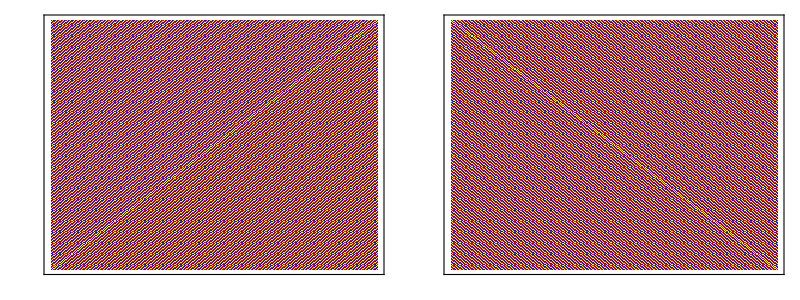

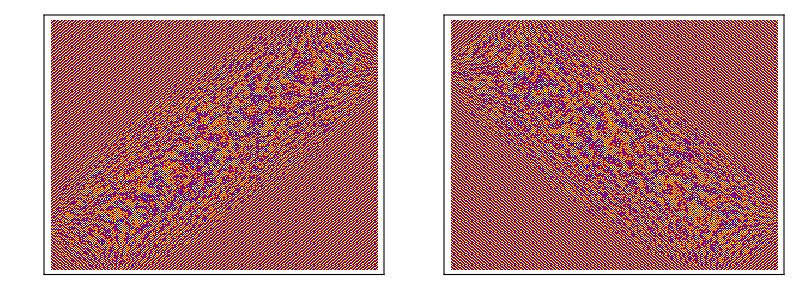

```mathematica
{initial2731, initial2732} = Import[NotebookDirectory[], "output files/coupling_273/log_0.mx"];
Grid[{{ArrayPlot[initial2731, ColorRules -> colourRules, Frame->True], ArrayPlot[initial2732, ColorRules -> colourRules, Frame->True]}}] 
{final2731, final2732} = Import[NotebookDirectory[], "output files/coupling_273/log_900000000.mx"];
Grid[{{ArrayPlot[final2731, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
(* NOTE: change input and stagger! *)
{time, step, {final2731max, final2732min}} = viewAfterSteps[dim, final2731, final2732, 2000000000, 10000000, 900000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final2731max, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732min, ColorRules -> colourRules, Frame->True]}}]
```

63812

63108

64031

63003

63330

63560

63753

63765

63206

63675

64021

63760

63754

63408

63567

63603

63689

63259

63505

63234

63369

63109

63232

62941

63115

63068

63300

63616

63209

63696

62775

62976

62545

62900

62803

62237

62847

63337

62530

62569

62799

62894

62914

63000

62921

63097

62497

62648

62723

62532

62435

$Aborted

DateString::arg: Argument time cannot be interpreted as a date or time input or as a date string format.

DateString[time,{Hour,:,Minute,:,Second}]

step steps

ArrayPlot::mat: Argument final2731max at position 1 is not a list of lists.

ArrayPlot::mat: Argument final2732min at position 1 is not a list of lists.

ArrayPlot[final2731max,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True] | ArrayPlot[final2732min,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True]

-Graphics-

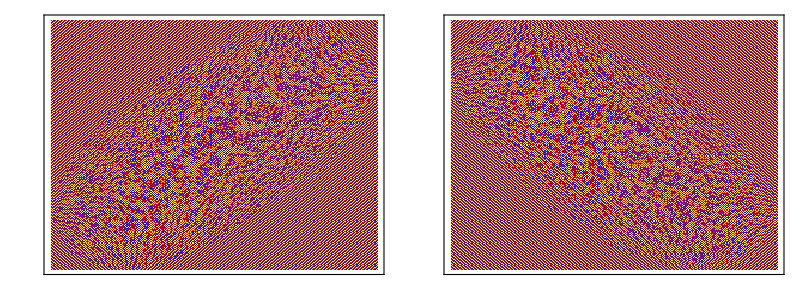

```mathematica
{initial2731, initial2732} = Import[NotebookDirectory[], "output files/coupling_273/log_0.mx"];
Grid[{{ArrayPlot[initial2731, ColorRules -> colourRules, Frame->True], ArrayPlot[initial2732, ColorRules -> colourRules, Frame->True]}}] 
{final2731, final2732} = Import[NotebookDirectory[], "output files/coupling_273/log_1400000000.mx"];
Grid[{{ArrayPlot[final2731, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
thisgrid = to3Colouring[generateMaxHeightGrid[273]];
```

```mathematica
ArrayPlot[thisgrid]
```

-Graphics-

```mathematica
Grid[{{ArrayPlot[thisgrid, ColorRules -> colourRules, Frame->True], ArrayPlot[to3Colouring[generateMinHeightGrid[273]], ColorRules -> colourRules, Frame->True]}}]
```

-Graphics-

```mathematica
{initial5111, initial5112} = Import[NotebookDirectory[], "output files/coupling_511/log_0.mx"];
Grid[{{ArrayPlot[initial5111, ColorRules -> colourRules, Frame->True], ArrayPlot[initial5112, ColorRules -> colourRules, Frame->True]}}] 
{final5111, final5112} = Import[NotebookDirectory[], "output files/coupling_511/log_660000000.mx"];
Grid[{{ArrayPlot[final5111, ColorRules -> colourRules, Frame->True], ArrayPlot[final5112, ColorRules -> colourRules, Frame->True]}}]
```

-Graphics- | -Graphics-

-Graphics- | -Graphics-

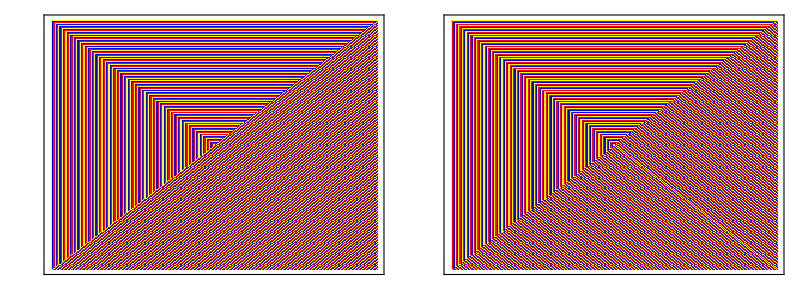

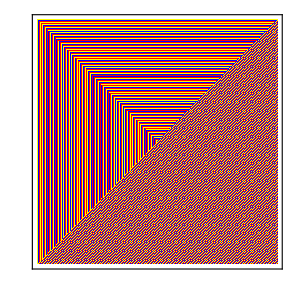
-Graphics- | -Graphics-

```mathematica
{initial1, initial2} = Import[NotebookDirectory[], "output files/coupling_273/log_0.mx"];
Grid[{{ArrayPlot[initial1, ColorRules -> colourRules, Frame->True], ArrayPlot[initial2, ColorRules -> colourRules, Frame->True]}}] 
{final2731, final2732} = Import[NotebookDirectory[], "output files/coupling_273/log_930000000.mx"];
Grid[{{ArrayPlot[final2731, ColorRules -> colourRules, Frame->True], ArrayPlot[final2732, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
dim = 511;
grid1 = to3Colouring[generateMaxHeightGrid[dim]];
grid2 = to3Colouring[generateMinHeightGrid[dim]];
(* NOTE: change input and stagger! *)
{time, step, {final5111max, final5112min}} = viewAfterSteps[dim, grid1, grid2, 1000000000, 10000000, 0];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final5111max, ColorRules -> colourRules, Frame->True], ArrayPlot[final5112min, ColorRules -> colourRules, Frame->True]}}]
```

$Aborted

00:27:20

28402849 steps

ArrayPlot::mat: Argument final5111max at position 1 is not a list of lists.

ArrayPlot::mat: Argument final5112min at position 1 is not a list of lists.

ArrayPlot[final5111max,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True] | ArrayPlot[final5112min,ColorRules→{0→RGBColor[1, 0, 0],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1]},Frame→True]

```mathematica
{intermediate5111, intermediate5112} = Import[NotebookDirectory[], "output files/coupling_511/log_570000000.mx"];
{time, step, {final5111max, final5112min}} = viewAfterSteps[dim, grid1, grid2, 1000000000, 10000000, 570000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final5111max, ColorRules -> colourRules, Frame->True], ArrayPlot[final5112min, ColorRules -> colourRules, Frame->True]}}]
```

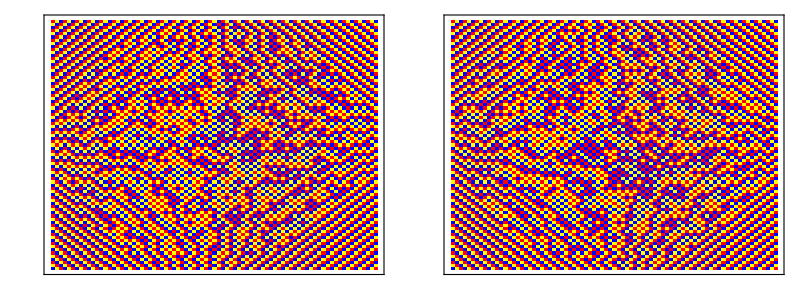

```mathematica
{final1, final2} = Import[NotebookDirectory[], "output files/coupling_81/log_57000000.mx"];
Grid[{{ArrayPlot[final1, ColorRules -> colourRules, Frame->True], ArrayPlot[final2, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
dim = 9;
minGrid = to3Colouring[generateMinHeightGrid[dim]];
oneStep[dim, maxGrid, minGrid]
(*MatrixForm[generateMaxHeightGrid[dim]]
MatrixForm[maxGrid]
MatrixForm[generateMinHeightGrid[dim]]
MatrixForm[minGrid]
coin = True; MatrixForm[to3Colouring[generateMinHeightGrid[dim]]]
site = {5,5};
Map[# = changeColour[#, site, Mod[coinSignAssociation[coin][#[[Sequence @@ site]], 2], 3]] &, {maxGrid, minGrid}]
Map[If[coinFunctionAssociation[coin][#, site], changeColour[#, site, Mod[coinSignAssociation[coin][#[[Sequence @@ site]], 2], 3]]] &, {maxGrid, minGrid}];
(*If[coinFunctionAssociation[coin][minGrid, site], minGrid = changeColour[minGrid, site, Mod[coinSignAssociation[coin][minGrid[[Sequence @@ site]], 2], 3]]]*)*)
(*MatrixForm[maxGrid]
MatrixForm[minGrid]*)
```

{{{0,1,2,0,1,2,0,1,2},{1,2,0,1,2,0,1,2,1},{2,0,1,2,0,1,2,1,0},{0,1,2,0,1,2,1,0,2},{1,2,0,1,2,1,0,2,1},{2,0,1,2,1,0,2,1,0},{0,1,2,1,0,2,1,0,2},{1,2,1,0,2,1,0,2,1},{2,1,0,2,1,0,2,1,0}},{{0,1,2,0,1,2,0,1,2},{1,0,1,2,0,1,2,0,1},{2,1,0,1,2,0,1,2,0},{0,2,1,0,1,2,0,1,2},{1,0,2,1,0,1,2,0,1},{2,1,0,2,1,0,1,2,0},{0,2,1,0,2,1,0,1,2},{1,0,2,1,0,2,1,0,1},{2,1,0,2,1,0,2,1,0}}}

(0 | 1 | 2 | 0 | 1 | 2 | 0 | 1 | 2
1 | 2 | 0 | 1 | 2 | 0 | 1 | 2 | 1
2 | 0 | 1 | 2 | 0 | 1 | 2 | 1 | 0
0 | 1 | 2 | 0 | 1 | 2 | 1 | 0 | 2
1 | 2 | 0 | 1 | 2 | 1 | 0 | 2 | 1
2 | 0 | 1 | 2 | 1 | 0 | 2 | 1 | 0
0 | 1 | 2 | 1 | 0 | 2 | 1 | 0 | 2
1 | 2 | 1 | 0 | 2 | 1 | 0 | 2 | 1
2 | 1 | 0 | 2 | 1 | 0 | 2 | 1 | 0)

(0 | 1 | 2 | 0 | 1 | 2 | 0 | 1 | 2
1 | 0 | 1 | 2 | 0 | 1 | 2 | 0 | 1
2 | 1 | 0 | 1 | 2 | 0 | 1 | 2 | 0
0 | 2 | 1 | 0 | 1 | 2 | 0 | 1 | 2
1 | 0 | 2 | 1 | 0 | 1 | 2 | 0 | 1
2 | 1 | 0 | 2 | 1 | 0 | 1 | 2 | 0
0 | 2 | 1 | 0 | 2 | 1 | 0 | 1 | 2
1 | 0 | 2 | 1 | 0 | 2 | 1 | 0 | 1
2 | 1 | 0 | 2 | 1 | 0 | 2 | 1 | 0)